```mathematica
chi=13.6 1.6 10^-12;
k = 1.38 10^-16;
T=10000;
chi/(k T)
```

15.7681

```mathematica
chi2=4.27 1.6 10^-12;
```

```mathematica
T2=1000;
```

```mathematica
phi[x_]:=2.5+chi/(k T)
phi2[x_]:=2.5+chi2/(k T2)
```

```mathematica
delad[x_]:=(2+x (1-x) phi[x])/(5+x (1-x) phi[x]^2)
```

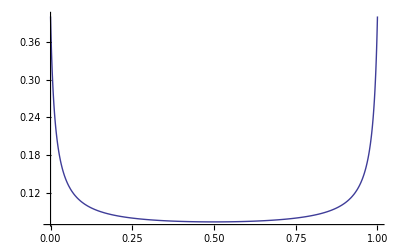

```mathematica
Plot[delad[x], {x, 0, 1}, PlotRange->All]
```

```mathematica
Clear[chi2, k, T2]
```

```mathematica
delad2[x_]:=(1+x+x/2 (1-x^2) chi2 / (k T2)) / (5 x + 7/2 (1-x) +x(1-x^2)/2 (chi2 /(k T2))^2)
```

```mathematica
delad2[x]
```

(1+x+(chi2 x (1-x^2))/(2 k T2))/((7 (1-x))/2+5 x+(chi2^2 x (1-x^2))/(2 k^2 T2^2))

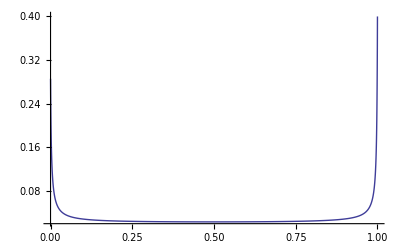

```mathematica
Plot[delad2[x], {x, 0, 1}, PlotRange->All]
```

```mathematica
delad2[1]
```

0.4

```mathematica
thetar=85;
```

```mathematica
Clear[T]
```

```mathematica
Clear[thetar]
```

```mathematica
Zrpara50=1/2∑_(j=0)^50 (1+(-1)^j)(2 j+1) Exp[-j (j+1) thetar/T];
upara50=T^2D[Log[Zrpara50], T];
Cvpara50=D[upara50, T];
```

```mathematica
Zr[T_]:=(2-(-1)^j)(2 j+1) Exp[-j (j+1) thetar/T]
```

```mathematica
Clear[Zr]
```

```mathematica
u=T^2D[Log[Zr[T]], T]
Cv=D[u, T]
```

j (1+j) thetar

0

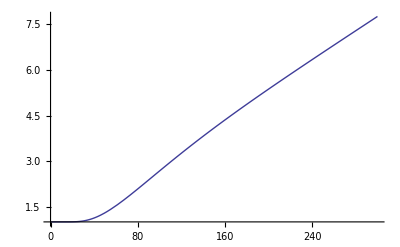

```mathematica
Plot[Zr50, {T, 0, 300}, PlotRange->All]
```

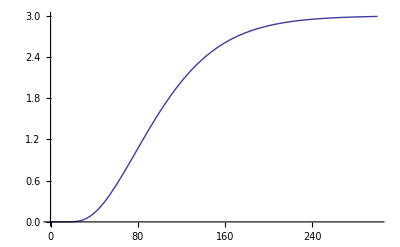

```mathematica
Plot[Zrortho50/Zrpara50, {T, 0, 300}, PlotRange->All]
```

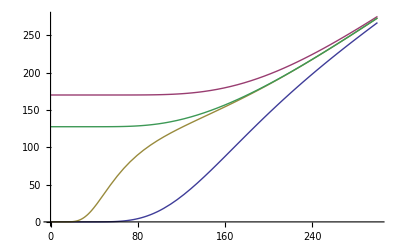

```mathematica
Plot[{upara50, uortho50, u50, ur31ratio50}, {T, 0, 300}, PlotRange->All]
```

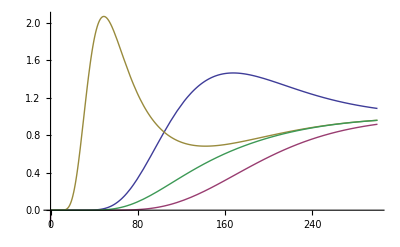

```mathematica
Plot[{Cvpara50,  Cvortho50, Cv50, Cv31ratio50}, {T, 0, 300}, PlotRange->All]
```

```mathematica
Zrortho50=3/2∑_(j=0)^50 (1-(-1)^j)(2 j+1) Exp[-j (j+1) thetar/T];
uortho50=T^2D[Log[Zrortho50], T];
Cvortho50=D[uortho50, T];
```

```mathematica
Zr50=∑_(j=0)^50 (2-(-1)^j)(2 j+1) Exp[-j (j+1) thetar/T];
u50=Zrpara50/Zr50 upara50+Zrortho50/Zr50 uortho50;
(*u50=T^2D[Log[Zr50], T];*)
Cv50=D[u50, T];
```

```mathematica
ur31ratio50=1/4 upara50+3/4 uortho50;
Cv31ratio50=D[ur31ratio50, T];
```

```mathematica
4.48 1.6 10^-12/1.38/10^-16
```

51942.

```mathematica
Exp[-4.48 1.6 10^-12/1.38/10^-16/1500]
```

9.14623×10^-16

```mathematica
(Pi 1.67 10^-24 k 1500)^1.5 2.35 1.67 10^-24/(6.6 10^-27)^3 / 10^-12
```

1.54493×10^13